((1-Cos[i]) Sin[i])/(1+Cos[i])^2+Sin[i]/(1+Cos[i])

(2 √γ ((√(1-(1-γ)^2/(1+γ)^2) (1-(1-γ)/(1+γ)))/(1+(1-γ)/(1+γ))^2+(√(1-(1-γ)^2/(1+γ)^2))/(1+(1-γ)/(1+γ))))/(1+γ)

2 γ

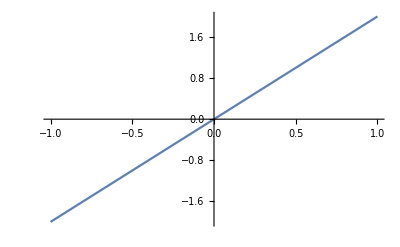

```mathematica
D[(1-Cos[i])/(1 + Cos[i]),i]
% * (2 Sqrt[γ])/(1 +γ) /. {i -> ArcCos[(1-γ)/(1+γ)]}
Simplify[% , Assumptions->{γ> -1, γ< 1}]
Plot[%,{γ,-1,1}]
```

```mathematica
((1-Cos[i]) Sin[i])/(1+Cos[i])^2+Sin[i]/(1+Cos[i])
```

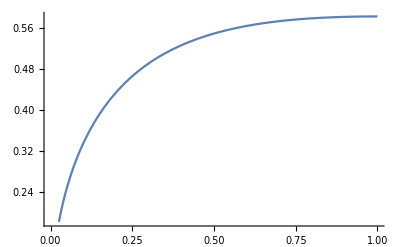

```mathematica
Plot[1/(4-π)Sqrt[x]/(1+x),{x,0,1}]
```

```mathematica
Integrate[1/(4-π)Sqrt[x]/(1+x),{x,0,1}]
```

1/2

```mathematica
P = (1/(2 - π/2))^4 Sqrt[g1d g2d g1b g2b]/((1+g1d)(1+g2d)(1+g1b)(1+g2b))
D[D[Log[P], g1d], g2d]
```

(√(g1b g1d g2b g2d))/((1+g1b) (1+g1d) (1+g2b) (1+g2d) (2-π/2)^4)

1/(√(g1b g1d g2b g2d))(1+g1b) (1+g1d) (1+g2b) (1+g2d) (-(g1b g2b g2d)/(2 (1+g1b) (1+g1d) (1+g2b) √(g1b g1d g2b g2d) (1+g2d)^2 (2-π/2)^4)+(√(g1b g1d g2b g2d))/((1+g1b) (1+g1d)^2 (1+g2b) (1+g2d)^2 (2-π/2)^4)-(g1b^2 g1d g2b^2 g2d)/(4 (1+g1b) (1+g1d) (1+g2b) (g1b g1d g2b g2d)^(3/2) (1+g2d) (2-π/2)^4)-(g1b g1d g2b)/(2 (1+g1b) (1+g1d)^2 (1+g2b) √(g1b g1d g2b g2d) (1+g2d) (2-π/2)^4)+(g1b g2b)/(2 (1+g1b) (1+g1d) (1+g2b) √(g1b g1d g2b g2d) (1+g2d) (2-π/2)^4)) (2-π/2)^4+1/(√(g1b g1d g2b g2d))(1+g1b) (1+g1d) (1+g2b) ((g1b g2b g2d)/(2 (1+g1b) (1+g1d) (1+g2b) √(g1b g1d g2b g2d) (1+g2d) (2-π/2)^4)-(√(g1b g1d g2b g2d))/((1+g1b) (1+g1d)^2 (1+g2b) (1+g2d) (2-π/2)^4)) (2-π/2)^4-(g1b (1+g1b) g1d (1+g1d) g2b (1+g2b) (1+g2d) ((g1b g2b g2d)/(2 (1+g1b) (1+g1d) (1+g2b) √(g1b g1d g2b g2d) (1+g2d) (2-π/2)^4)-(√(g1b g1d g2b g2d))/((1+g1b) (1+g1d)^2 (1+g2b) (1+g2d) (2-π/2)^4)) (2-π/2)^4)/(2 (g1b g1d g2b g2d)^(3/2))

```mathematica
i = ArcCos[(1 - γ)/(1 + γ)]
D[i,γ] 
Simplify[%]
```

ArcCos[(1-γ)/(1+γ)]

-(-(1-γ)/(1+γ)^2-1/(1+γ))/(√(1-(1-γ)^2/(1+γ)^2))

(√(γ/(1+γ)^2))/γ

```mathematica
γ == (q-1)/(q+1)
Solve[%,q]
```

γ==(-1+q)/(1+q)

{{q→(-1-γ)/(-1+γ)}}

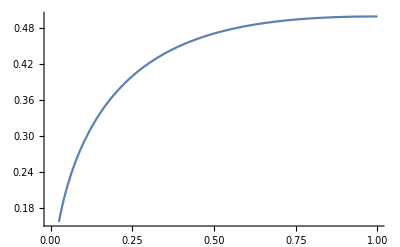

```mathematica
Plot[(√γ)/(1 + γ),{γ,0,1}]
```